```mathematica
(*Plotting in 3D*)
r[t_]:={t Cos[t], t Sin[t], t}
maxT = 10;
ParametricPlot3D[r[tt],{tt,0,100}]
Manipulate[
Show[
(*The function plot*)
ParametricPlot3D[r[tt],{tt,0,maxT}],
(*The current point plot*)
ListPointPlot3D[{r[t]}, PlotRange->Full, PlotStyle->Orange],
(*The radius vector plot*)
Graphics3D[Arrow[{{0,0,0},r[t]}], PlotRange->Full],
(*The derivative vector plot*)
Graphics3D[{Red,Arrow[{r[t],r[t]+r'[t]}], PlotRange->Full}],
(*The unit derivative vector plot*)
Graphics3D[{Green,Arrow[{r[t],r[t]+Normalize[r'[t]]}], PlotRange->Full}]
],
{t,0,maxT}
]
```

-Graphics3D-

ParametricPlot3D::plln: Limiting value maxT in {tt,0,maxT} is not a machine-sized real number.

ListPointPlot3D::arrayerr: {r[8.36]} must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[r[tt],{tt,0,maxT}],ListPointPlot3D[{r[8.36]},PlotRange→Full,PlotStyle→RGBColor[1, 0.5, 0]],,,].

ParametricPlot3D::plln: Limiting value maxT in {tt,0,maxT} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[r[tt],{tt,0,maxT}],ListPointPlot3D[{r[8.36]},PlotRange→Full,PlotStyle→RGBColor[1, 0.5, 0]],,,].

ParametricPlot3D::plln: Limiting value maxT in {tt,0,maxT} is not a machine-sized real number.

ListPointPlot3D::arrayerr: {r[8.36]} must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[r[tt],{tt,0,maxT}],ListPointPlot3D[{r[8.36]},PlotRange→Full,PlotStyle→RGBColor[1, 0.5, 0]],,,].

ParametricPlot3D::plln: Limiting value maxT in {tt,0,maxT} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[r[tt],{tt,0,maxT}],ListPointPlot3D[{r[8.36]},PlotRange→Full,PlotStyle→RGBColor[1, 0.5, 0]],,,].

ParametricPlot3D::plln: Limiting value maxT in {tt,0,maxT} is not a machine-sized real number.

ListPointPlot3D::arrayerr: {r[8.36]} must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[r[tt],{tt,0,maxT}],ListPointPlot3D[{r[8.36]},PlotRange→Full,PlotStyle→RGBColor[1, 0.5, 0]],,,].

ParametricPlot3D::plln: Limiting value maxT in {tt,0,maxT} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[r[tt],{tt,0,maxT}],ListPointPlot3D[{r[8.36]},PlotRange→Full,PlotStyle→RGBColor[1, 0.5, 0]],,,].

BezierFunction[…]

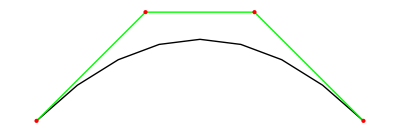

True

True

{{6,5},{1,4.5},{1,0.5},{5,0}}

{{5,0},{9,-0.5},{9,-4.5},{4,-5}}

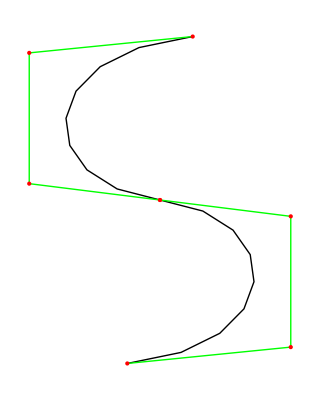

```mathematica
(*Splines model*)
controlPoints = {{1,1}, {2,2}, {3,2}, {4,1}};

(*Control points for the letter C*)
(*controlPoints = {{5,5}, {1,4.5}, {1,0.5}, {5,0}};*)
bezier = BezierCurve[controlPoints];
bezierFunction = BezierFunction[controlPoints]
Graphics[{bezier,Green,Line[controlPoints],Red,Point[controlPoints]}]
(*Proof of tangentiality *)
Normalize[controlPoints[[2]]-First[controlPoints]] == Normalize[bezierFunction'[0]]
Normalize[Last[controlPoints]-controlPoints[[Length[controlPoints]-1]]] == Normalize[bezierFunction'[1]]

(*Control points for the upper part of the letter S*)
controlPoints1 = {{6,5}, {1,4.5}, {1,0.5}, {5,0}}
upperSPart =Graphics[{BezierCurve[controlPoints1],Green,Line[controlPoints1],Red,Point[controlPoints1]}]; 
(*Control points for the lower part of the letter S*)
controlPoints2 = {{5,0}, {9,-0.5}, {9,-4.5}, {4,-5}}
lowerSPart =Graphics[{BezierCurve[controlPoints2],Green,Line[controlPoints2],Red,Point[controlPoints2]}]; 
Show[upperSPart,lowerSPart]
```

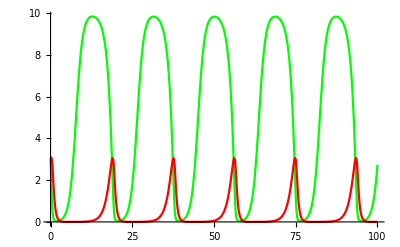

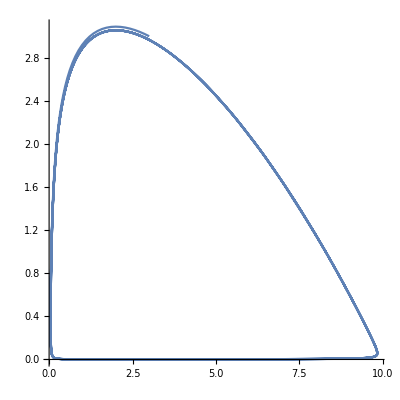

```mathematica
(*Predator-Prey model *)
Clear[p]
Clear[n]
r=1;
K=10;
b=1;
a=3;
λ=1;
c=2;
Subscript[p, 0]=3;
Subscript[n, 0]=3;
maxT=100;
dndt[t_]:=r n[t](1-n[t]/K)-p[t]a n[t]/(b+n[t])
dpdt[t_]:=-c p[t]+λ p[t]a n[t]/(b+n[t])
(*system = {n'[t],p'[t]}=={dndt[t],dpdt[t]}*)
sol = NDSolveValue[{n'[t]==dndt[t],p'[t]==dpdt[t],p[0]==Subscript[p, 0],n[0]==Subscript[n, 0]}, {n,p},{t,0,maxT}];
n:=sol[[1]];
p:=sol[[2]];
preyPlot=Plot[n[t],{t,0,maxT},PlotStyle->Green, PlotRange->All,AxesOrigin->{0,0}];
predatorPlot=Plot[p[t],{t,0,maxT},PlotStyle->Red, PlotRange->All,AxesOrigin->{0,0}];
Show[preyPlot,predatorPlot]
ParametricPlot[{n[t],p[t]},{t,0,maxT}, PlotRange->All,AxesOrigin->{0,0},AspectRatio->1]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

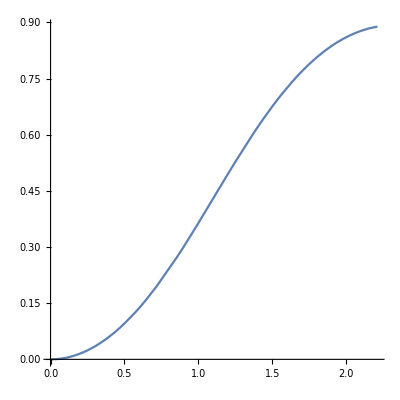

```mathematica
(*Drop Model*)
Clear[r]
Clear[z]
Clear[θ]
b=13/10;
Subscript[ϵ, g]=-1;
B=2.4;
Subscript[r, 0]=0;
Subscript[z, 0]=0;
Subscript[θ, 0]=0;
maxS=30;
drds[s_]:=Cos[θ[s]]
dzds[s_]:=Sin[θ[s]]
dθds[s_]:=If[s>$MachineEpsilon,2/b-Sin[θ[s]]/r[s]+Subscript[ϵ, g] B z[s],1/b]
sol = NDSolveValue[{
r'[s]==drds[s],
z'[s]==dzds[s],
θ'[s]==dθds[s],
r[0]==Subscript[r, 0],z[0]==Subscript[z, 0],θ[0]==Subscript[θ, 0]}, 
{r,z,θ},
{s,0,maxS}]
r:=sol[[1]];
z:=sol[[2]];

ParametricPlot[{r[s],z[s]},{s,0,maxS},RegionFunction->Function[{s},r[s]≤1], PlotRange->All,AxesOrigin->{0,0},AspectRatio->1]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

{5.09858,{t→1.01972}}

2.03943

35.324

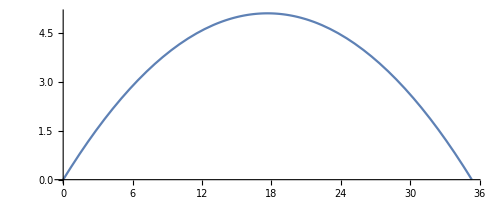

```mathematica
(*Cannon ball*)
Clear[x]
Clear[y]
Clear[vx]
Clear[vy]
g=9.80665;
κ=0;
m=5;
Subscript[v, 0]=20;
α=Pi/6;
Subscript[vx, 0]=Subscript[v, 0] Cos[α];
Subscript[vy, 0]=Subscript[v, 0] Sin[α];
maxT=3;
(*dvxdt[t_]:=-κ Norm[{vx[t],vy[t]}]/m vx[t]
dvydt[t_]:=-g-κ Norm[{vx[t],vy[t]}]/m vy[t]
sol = NDSolveValue[{vx'[t]==dvxdt[t],vy'[t]==dvydt[t],vx[0]==Subscript[vx, 0],vy[0]==Subscript[vy, 0]}, {vx,vy},{t,0,maxT}]*)
dvxdt[t_]:=-κ Norm[{vx[t],vy[t]}]/m vx[t]
dvydt[t_]:=-g-κ Norm[{vx[t],vy[t]}]/m vy[t]
sol = NDSolveValue[{
x'[t]==vx[t],
vx'[t]==dvxdt[t],
y'[t]==vy[t],
vy'[t]==dvydt[t],
x[0]==0,vx[0]==Subscript[vx, 0],y[0]==0,vy[0]==Subscript[vy, 0]}, 
{x,vx,y,vy},
{t,0,maxT}]
x:=sol[[1]];
y:=sol[[3]];

FindMaximum[y[t],t]
fallT=t/.FindRoot[y[t],{t,maxT}]
x[fallT]
(*NSolve[{t<maxT,y[t]==0,t>$MachineEpsilon},t]*)
ParametricPlot[{x[t],y[t]},{t,0,fallT},
PlotRange->All,AxesOrigin->{0,0},ImageSize->Full]
```